# Tips & Tricks: Mathematica for Research

## Lecture 2 (15/04/2026)

```mathematica
Quit[]
```

```mathematica
SetOptions[EvaluationNotebook[],Magnification->1.75]
```

## Question from last time...

```mathematica
(* a_ vs a__ vs a___ *)
```

```mathematica
{a,b,c,d,e,f}/.{{left_,c,right_}:>{c,right}}(*No match*)
{a,b,c,d,e,f}/.{{left__,c,right__}:>{c,right}}(*Match*)
{a,b,c,d,e,f}/.{{left__,a,right__}:>{right}}(*No match*)
{a,b,c,d,e,f}/.{{left___,a,right___}:>{right}}(*Match*)
```

{a,b,c,d,e,f}

{c,d,e,f}

{a,b,c,d,e,f}

{b,c,d,e,f}

```mathematica
γ[b]·γ[a]·"(stuff on the right)"/.{c___·γ[a_]·γ[b_]·d__:>c·(-γ[b]·γ[a]+2g[a,b])·d/;!OrderedQ[{a,b}]}
γ[b]·γ[a]·"(stuff on the right)"/.{c__·γ[a_]·γ[b_]·d__:>c·(-γ[b]·γ[a]+2g[a,b])·d/;!OrderedQ[{a,b}]}
```

(-γ[a]·γ[b]+2 g[b,a])·(stuff on the right)

γ[b]·γ[a]·(stuff on the right)

```mathematica
(*Optional/Default*)
```

```mathematica
{x,2x,3x}/.{a_ x:>a}
{x,2x,3x}/.{a_. x:>a}
```

{x,2,3}

{1,2,3}

```mathematica
??Times
```

```mathematica
{x,x^2,x^3}/.{x^a_:>a}
{x,x^2,x^3}/.{x^(a_.):>a}
```

{x,2,3}

{1,2,3}

```mathematica
??Power
```

## Wick contraction & Feynman diagrams

```mathematica
<<Notation`
```

```mathematica
Notation[Subscript[q, a_] ⟺ q[a_]]
```

```mathematica
ClearAll[vertex]
vertex[n_]:=Block[{a=Unique[a]},Product[ϕ[Subscript[k, a[i]]],{i,1,n}]]
```

```mathematica
ClearAll[wick]
wick[X_Times]:=Block[{},Sum[⟨X[[1]],X[[j]]⟩wick[Drop[Drop[X,{j}],{1}]],{j,2,Length[X]}]//Expand];
wick[ϕ[a_]ϕ[b_]]:=⟨ϕ[a],ϕ[b]⟩
```

```mathematica
ClearAll[tograph]
tograph[term_]:=Graph[Sort@(List@@term/.{⟨ϕ[Subscript[k, a_]],ϕ[Subscript[k, b_]]⟩:>a[[0]]<->b[[0]]}),VertexLabels->{_?IntegerQ->Automatic},BaseStyle->Black,ImageSize->200]
```

```mathematica
exp=ϕ[Subscript[k, 1[]]]ϕ[Subscript[k, 2[]]]vertex[3]vertex[3]vertex[4] ϕ[Subscript[k, 3[]]] ϕ[Subscript[k, 4[]]];
```

```mathematica
wicked=wick[exp];
wicked//Length
```

135135

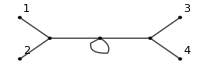
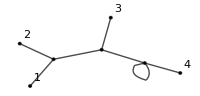
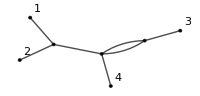
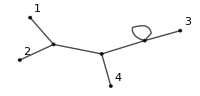
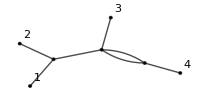
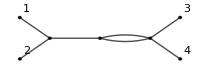
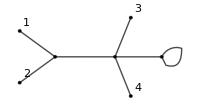
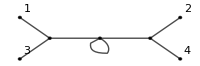
-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1Feynman Diagrams for ϕϕ ⟶ ϕϕ with λ_3/(3!)ϕ^3+λ_4/(4!)ϕ^4 at O(λ_3^2λ_4)

```mathematica
diagrams=Labeled[(tograph/@wicked/.{G_Graph:>0/;!ConnectedGraphQ[G]})/.{a_ G_Graph:>Labeled[G,a/(3!3!4!),Left,LabelStyle->{20}]},"Feynman Diagrams for ϕϕ ⟶ ϕϕ with λ_3/(3!)ϕ^3+λ_4/(4!)ϕ^4 at O(λ_3^2λ_4)",Top,LabelStyle->{16},Spacings->{Automatic,5}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["diagrams.pdf",diagrams]
SystemOpen["diagrams.pdf"]
```

/Users/brunovaleixobento/Library/CloudStorage/OneDrive-UniversidadedeLisboa/Madrid/IFT/Mathematica Lectures/Lectures

diagrams.pdf

```mathematica
Labeled[(Monitor[Sum[If[ConnectedGraphQ[#],1/(3!3!4!)#,0]&@(tograph[wicked[[i]]]),{i,1,Length[wicked]}],Grid@{{ProgressIndicator[i,{1,Length[wicked]}],i,Length[wicked]}}])/.{a_ G_Graph:>Labeled[G,a,Left,LabelStyle->{20}]},"Feynman Diagrams for ϕϕ ⟶ ϕϕ with λ_3/(3!)ϕ^3+λ_4/(4!)ϕ^4 at O(λ_3^2λ_4)",Top]
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2+-Graphics-1/2Feynman Diagrams for ϕϕ ⟶ ϕϕ with λ_3/(3!)ϕ^3+λ_4/(4!)ϕ^4 at O(λ_3^2λ_4)

### Others

```mathematica
Directory[]
```

/Users/brunovaleixobento/Library/CloudStorage/OneDrive-UniversidadedeLisboa/Madrid/IFT/Mathematica Lectures/Lectures

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/brunovaleixobento/Library/CloudStorage/OneDrive-UniversidadedeLisboa/Madrid/IFT/Mathematica Lectures/Lectures

```mathematica
1//Head
a$24100[3]//Head
```

Integer

a$24100

```mathematica
a$24100[3][[0]]
a$24100[4][[0]]
```

a$24100

a$24100

```mathematica
wicked[[1]]
```

⟨ϕ[k_(1[])],ϕ[k_a$53512[4]]⟩ ⟨ϕ[k_(2[])],ϕ[k_a$53512[3]]⟩ ⟨ϕ[k_a$53512[1]],ϕ[k_a$53512[2]]⟩

```mathematica
tograph/@wicked
```

3 -Graphics-+12 -Graphics-

```mathematica
tograph[wicked[[1]]]
```

-Graphics-

```mathematica
List@@wicked[[1]]/.{⟨ϕ[Subscript[k, a_]],ϕ[Subscript[k, b_]]⟩:>a[[0]]<->b[[0]]}
Graph[%,VertexLabels->{_?IntegerQ->Automatic}]
```

{1<->a$53512,2<->a$53512,a$53512<->a$53512}

-Graphics-

```mathematica
?Graph
```

```mathematica
wick[ϕ[1]+ϕ[2]]
```

wick[ϕ[1]+ϕ[2]]

```mathematica
wick[exp]//Length
```

15

```mathematica
exp[[0]]
```

Times

```mathematica
exp
Drop[Drop[exp,{2}],{1}]
```

ϕ[k_1] ϕ[k_2] ϕ[k_a$24100[1]] ϕ[k_a$24100[2]] ϕ[k_a$24100[3]] ϕ[k_a$24100[4]]

ϕ[k_a$24100[1]] ϕ[k_a$24100[2]] ϕ[k_a$24100[3]] ϕ[k_a$24100[4]]

```mathematica
exp/.{exp[[0]]->List}
List@@exp
```

{ϕ[k_1],ϕ[k_2],ϕ[k_a$24100[1]],ϕ[k_a$24100[2]],ϕ[k_a$24100[3]],ϕ[k_a$24100[4]]}

{ϕ[k_1],ϕ[k_2],ϕ[k_a$24100[1]],ϕ[k_a$24100[2]],ϕ[k_a$24100[3]],ϕ[k_a$24100[4]]}

```mathematica
Subscript[q, 3]//FullForm
```

Subscript[q,3]

```mathematica
Unique[a]
```

a$20486